```mathematica
Remove["Global`*"]
```

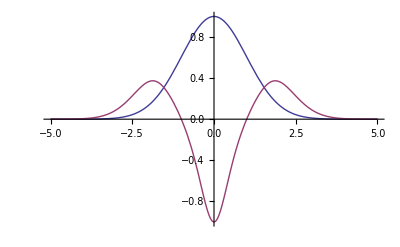

```mathematica
testFunc[x_,a_] = Exp[-x^2/(2a^2)];
curvatureTestFunc[x_,a_] = D[testFunc[x,a],x,x]/(1+D[testFunc[x,a],x]^2)^(3/2);
Plot[{testFunc[x,1], curvatureTestFunc[x,1]},{x,-5,5}, PlotRange->Full]
```

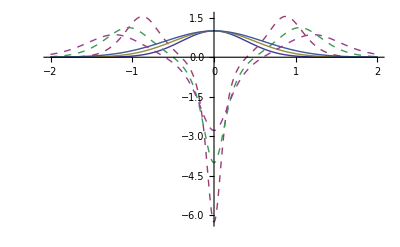

```mathematica
Plot[Evaluate@Table[{testFunc[x,a], curvatureTestFunc[x,a]},{a,.4,.6,.1}],{x,-2,2}, PlotRange->Full, PlotStyle->{Thick, Dashed}]
```

```mathematica
Manipulate[Plot[{testFunc[x,a], curvatureTestFunc[x,a]},{x,-2,2}, PlotRange->Full],{a,.1,1,.1}]
```

```mathematica
x[t_,a_] = Exp[-a*t]*Cos[4t]
Manipulate[Plot[x[t,a],{t,-Pi,Pi}],{a,.1,.5}]
```

ⅇ^(-a t) Cos[4 t]

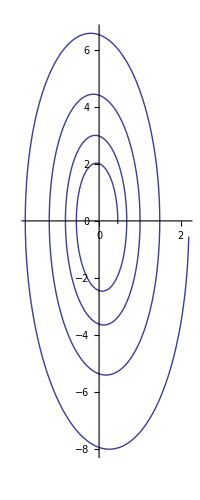

```mathematica
x[t_,a_] = Exp[-a*t]*Cos[4t];
p[t_,a_] = D[x[t,a],t];
ParametricPlot[{x[t,.25],p[t,.25]},{t,-Pi,Pi}]
```

```mathematica
Remove["Global`*"]
```

Radiation Pattern of a moving charge. 
# in the case when the velocity is parallel to the acceleration of the moving charge.

```mathematica
Manipulate[PolarPlot[{Sin[x]^2/(1-(i)*Cos[x])^5},{x,0,2Pi}],{i,0,1}]
```

# in the case when the velocity if perpenicular to the acceleration of the moving charge and phi or y is  an integral multiple of Pi. in this case beta - velocity, beta dot - acceleration and n - the radial vector  are all in the same plane.

```mathematica
Manipulate[PolarPlot[{1/(1-(i)*Cos[x])^3},{x,0,2Pi}],{i,0,1}]
```

# in the case when the velocity if perpenicular to the acceleration of the moving charge and phi or y is  (2n+1)Pi/2. in this case, beta - velocity, beta dot - acceleration and n - the radial vector  are all in three mutually perpendicular planes.

```mathematica
Manipulate[PolarPlot[{1/(1-(i)*Cos[x])^3*(1-Sin[x]^2*(1-i*i)/(1-i*Cos[x])^2)},{x,0,2Pi}],{i,0,1}]
```

# a 3D plot of the radiation pattern of a moving charge in the case when the velocity is perpendicular to the acceleration of the charge and the dependence of the pattern on beta - the ratio of V/c.

```mathematica
Manipulate[SphericalPlot3D[1/(1-(i)*Cos[x])^3*(1-Cos[y]^2*Sin[x]^2*(1-i*i)/(1-i*Cos[x])^2),{y,0,2Pi},{x,0,2Pi}],{i,0,1}]
```

```mathematica
Remove["Global`*"]
```

```mathematica
testFunc[x_, y_] = x^2+y^2;
Plot3D[testFunc[x,y],{x,-4,4}, {y,-4,4}]
```

-Graphics3D-

```mathematica
Remove["Global`*"]
```

```mathematica
testFunc[x_, y_] = (x^2+y^2)^(1/2);
Plot3D[{testFunc[x,y], -testFunc[x,y]},{x,-4,4},{y,-4,4}]
```

-Graphics3D-

```mathematica
testFunc1[x_, y_] = (-1 + (x^2+y^2))^(1/2);
Plot3D[{testFunc1[x,y], -testFunc1[x,y]},{x,-4,4},{y,-4,4}]
```

-Graphics3D-